# MEP Predictions

## Earth (Virgo, Lorenz)

### Quantities

```mathematica
k=Quantity[1,"BoltzmannConstant"]
```

1 k

```mathematica
σ=Quantity[1,"StefanBoltzmannConstant"]
```

1 σ

```mathematica
Ie=Quantity[300,"Watts"/"Meters"^2]Quantity[(2/6 π +√3)(6370)^2,"Kilometers"^2]
```

12173070000000000 (√3+π/3) W

```mathematica
Ip=Quantity[170,"Watts"/"Meters"^2]Quantity[(π -(2/6 π +√3))6370^2,"Kilometers"^2]
```

6898073000000000 (-√3+(2 π)/3) W

```mathematica
Te=Quantity[300,"Kelvins"]
```

300 K

```mathematica
Tp=Quantity[270,"Kelvins"]
```

270 K

```mathematica
Tsun=Quantity[5700,"Kelvins"]
```

5700 K

### Applying MEP

#### Standard way

```mathematica
fun=Q(((Ip+Q)/σ)^(-1/4)-((Ie-Q)/σ)^(-1/4))
```

Q (-1/((1 /σ) (-Q+12173070000000000 (√3+π/3) W))^(1/4)+1/((1 /σ) (Q+6898073000000000 (-√3+(2 π)/3) W))^(1/4))

```mathematica
Plot[fun,{Q,Quantity[0,"Watts"],Quantity[10^16,"Watts"]}]
```

-Graphics-

#### Including radiation entropy change

Including radiation entropy change, following comments by Essex...

```mathematica
fun2=Q(((Ip+Q)/σ)^(-1/4)-((Ie-Q)/σ)^(-1/4))+Ie((Ie-Q)/σ)^(-1/4)+Ip((Ip+Q)/σ)^(-1/4)-(Ie+Ip)/Tsun
```

-47/570 W/(m^2 K)+(170 W/m^2)/(((1 /σ) (Q+170 W/m^2))^(1/4))+(300 W/m^2)/(((1 /σ) (-Q+300 W/m^2))^(1/4))+Q (1/(((1 /σ) (Q+170 W/m^2))^(1/4))-1/(((1 /σ) (-Q+300 W/m^2))^(1/4)))

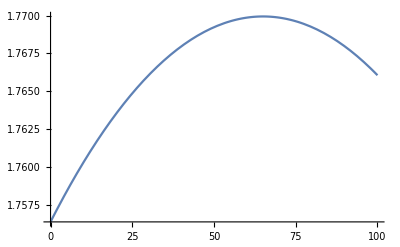

```mathematica
Plot[fun2,{Q,Quantity[0,"Watts"/"Meters"^2],Quantity[100,"Watts"/"Meters"^2]}]
```

Gives different results!

So my proposition would be to divide through the area through which the entropy is produced. For height of the atmosphere we take 8km.

```mathematica
fun3=(Q(((Ip+Q)/σ)^(-1/4)-((Ie-Q)/σ)^(-1/4)))/(Quantity[8 10^3,"Meters"]Quantity[6371 (√3)/2,"Meters"])+(Ie((Ie-Q)/σ)^(-1/4)+Ip((Ip+Q)/σ)^(-1/4)-(Ie+Ip)/Tsun)/(π Quantity[6371,"Meters"]Quantity[6371,"Meters"])
```

Q (1/(((1 /σ) (Q+170 W/m^2))^(1/4))-1/(((1 /σ) (-Q+300 W/m^2))^(1/4))) (1/(25484000 √3) per meter^2)+(-47/570 W/(m^2 K)+(170 W/m^2)/(((1 /σ) (Q+170 W/m^2))^(1/4))+(300 W/m^2)/(((1 /σ) (-Q+300 W/m^2))^(1/4))) (1/(40589641 π) per meter^2)

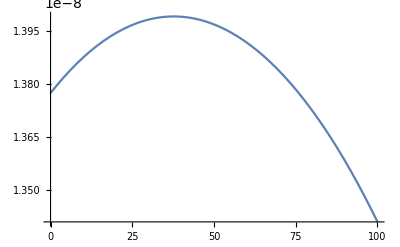

```mathematica
Plot[fun3,{Q,Quantity[0,"Watts"/"Meters"^2],Quantity[100,"Watts"/"Meters"^2]}]
```

Looks much better!

```mathematica
Subscript[E, I]=(1-0.26)*(2 π/6.0+√3)/(2π)*1373
```

449.417

```mathematica
Subscript[E, II]=(1-0.35)*(π-2*π/6-√3)/(2π)*1373
```

34.3111

```mathematica
2π (1-Cos[π/3])
```

π

```mathematica
Sin[2π/3]
```

(√3)/2

## Titan (Lorenz)

### Quantities

```mathematica
k=Quantity[1,"BoltzmannConstant"]
```

1 k

```mathematica
σ=Quantity[1,"StefanBoltzmannConstant"]
```

1 σ

```mathematica
Ie=0.01Quantity[300,"Watts"/"Meters"^2]
```

3. W/m^2

```mathematica
Ip=0.01Quantity[170,"Watts"/"Meters"^2]
```

1.7 W/m^2

```mathematica
Te=Quantity[93,"Kelvins"]
```

93 K

```mathematica
Tp=Quantity[89,"Kelvins"]
```

89 K

```mathematica
Tsun=Quantity[5700,"Kelvins"]
```

5700 K

### Applying MEP

#### Standard way

```mathematica
fun=Q(((Ip+Q)/σ)^(-1/4)-((Ie-Q)/σ)^(-1/4))
```

Q (1/(((1 /σ) (Q+1.7 W/m^2))^(1/4))-1/(((1 /σ) (-Q+3. W/m^2))^(1/4)))

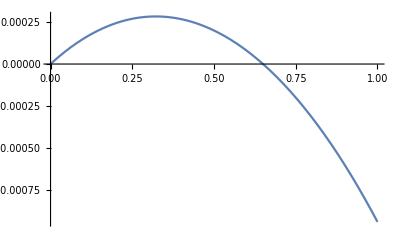

```mathematica
Plot[fun,{Q,Quantity[0,"Watts"/"Meters"^2],Quantity[1,"Watts"/"Meters"^2]}]
```

## Mars (Lorenz)

### Quantities

```mathematica
k=Quantity[1,"BoltzmannConstant"]
```

1 k

```mathematica
σ=Quantity[1,"StefanBoltzmannConstant"]
```

1 σ

```mathematica
Ie=Quantity[130,"Watts"/"Meters"^2]
```

130 W/m^2

```mathematica
Ip=Quantity[60,"Watts"/"Meters"^2]
```

60 W/m^2

```mathematica
Te=Quantity[93,"Kelvins"]
```

93 K

```mathematica
Tp=Quantity[89,"Kelvins"]
```

89 K

```mathematica
Tsun=Quantity[5700,"Kelvins"]
```

5700 K

### Applying MEP

#### Standard way

```mathematica
fun=Q(((Ip+Q)/σ)^(-1/4)-((Ie-Q)/σ)^(-1/4))
```

Q (1/(((1 /σ) (Q+60 W/m^2))^(1/4))-1/(((1 /σ) (-Q+130 W/m^2))^(1/4)))

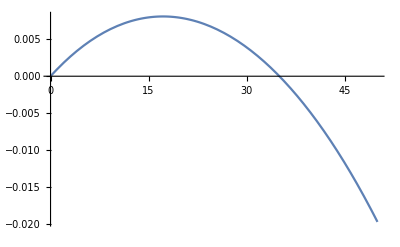

```mathematica
Plot[fun,{Q,Quantity[0,"Watts"/"Meters"^2],Quantity[50,"Watts"/"Meters"^2]}]
```